```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[]

styles={Directive[RGBColor[0,0,0],AbsoluteThickness[4]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0.5],AbsoluteThickness[2],AbsoluteDashing[{10,5}]],Directive[RGBColor[0,0.5,0],AbsoluteThickness[2],AbsoluteDashing[{10,5,2,5}]],Directive[RGBColor[1,0.5,0.0],AbsoluteThickness[2],AbsoluteDashing[{1,4}]],Directive[RGBColor[0.5,0.5,0.5],AbsoluteThickness[2],AbsoluteDashing[{1,4}]]};

FrameTicksFontSize=20;
FrameFontSize=20;PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[Black,FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]],Directive[Black,FontSize->FrameFontSize,FontFamily->"Times",AbsoluteThickness[1]]},AspectRatio->0.75,ImageSize->Medium,PlotStyle->styles,PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];

Nf=3;
eg=16Pi^2/30;
eq=6*3*7Pi^2/120;  (*check these later*)
sFac = eg+eq 

%*1.0

rationalPolyFit[data_,NN_,MM_]:=Module[{a,b,varsa,varsb,vars,sol,varsc,varsd,Q},
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[data,Sum[a[n]x^n,{n,0,NN}]/Sum[b[m]x^m,{m,0,MM}],vars,x,MaxIterations->10000];
varsc=varsa/.sol;
varsd=varsb/.sol;
Return[Sum[varsc[[n+1]]x^n,{n,0,NN}]/Sum[varsd[[m+1]]x^m,{m,0,MM}]];
];
```

/Users/Michael/Desktop/bjorken_vahydro/mathematica

(19 π^2)/12

15.6269

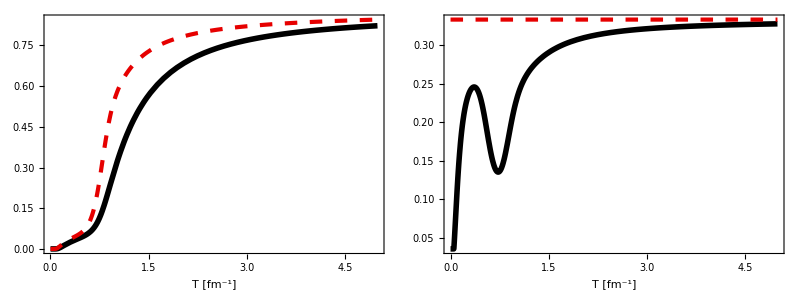

```mathematica
eosDataRaw=Import[wd<>"/eos.dat"];
eosData= Take[eosDataRaw,{3,Length[eosDataRaw]}];

(* Subscript[ϵ, eq](T) *)
LogEDLogTInt = Interpolation[eosData[[All,{1,2}]]];
edInt[T_] = 10^LogEDLogTInt[Log[10,T]];

(* Subscript[P, eq](T) *)
LogPLogTInt = Interpolation[eosData[[All,{1,4}]]];
PInt[T_] = 10^LogPLogTInt[Log[10,T]];


LogdPLogEdInt = Interpolation[eosData[[All,{2,5}]]];
dPIntE[e_]=10^LogdPLogEdInt[Log[10,e]];
LogdELogEdInt = Interpolation[eosData[[All,{2,3}]]];
dEIntE[e_]=10^LogdELogEdInt[Log[10,e]];

cs2Int[T_] = dPIntE[edInt[T]]/dEIntE[edInt[T]];

Grid[{{Plot[{PInt[T]/(sFac T^4/3),edInt[T]/(sFac T^4)},{T,.001,5},PlotStyle->styles,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{cs2Int[T],1/3},{T,0,5},PlotStyle->styles,ImageSize->400,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
```

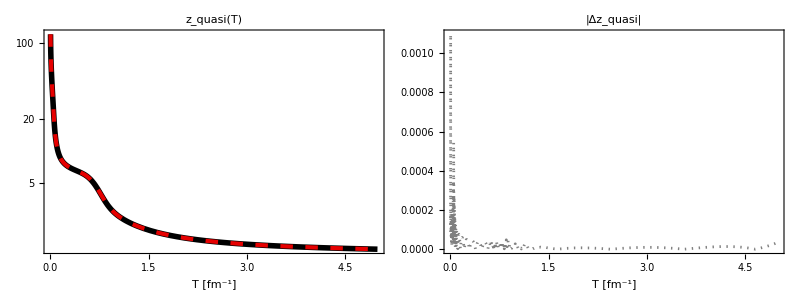

```mathematica
SInt[T_] = (edInt[T]+PInt[T])/T;
nc = 3.0;
nf = 3.0;
g =Pi^4/180.0*(4.0*(nc^2-1.0)+7.0*nc*nf);
F[T_]=(2.0*Pi^2)/g*SInt[T]/T^3;

zQuasi=Table[{T,""},{T,0.001,5.0,0.0005}];

zQuasi[[1,2]]=121.13801765177428;

For[i = 2, i ≤Length[zQuasi],i++,
zQuasi[[i,2]]=x/.FindRoot[x^3*BesselK[3,x]==F[zQuasi[[i,1]]],{x,zQuasi[[i-1,2]]},MaxIterations->2000];
]

zQuasifunc=Interpolation[zQuasi];

zQuasidata=Table[{T,zQuasifunc[T]},{T,0.001,5.0,0.0005}];

n = 18;

zQuasifit[T_]=rationalPolyFit[zQuasidata,n,n]/.{x->T};

Grid[{{
LogPlot[{zQuasifunc[T],zQuasifit[T]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["z_quasi(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{Abs[zQuasifunc[T]-zQuasifit[T]]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δz_quasi|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

zQuasifit[T]//CForm;
```

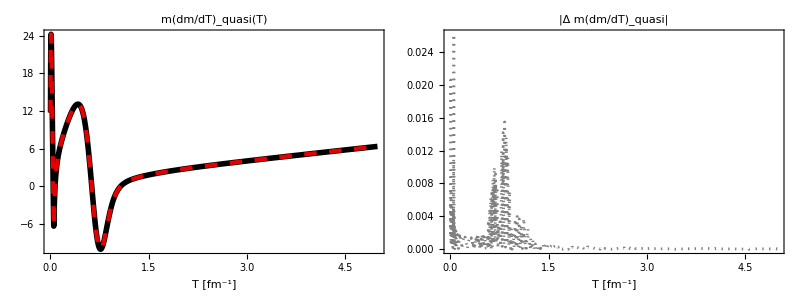

```mathematica
mQuasifunc[T_] =T*zQuasifunc[T]; 

mdmdTQuasi[T_] = mQuasifunc[T] * mQuasifunc'[T];

mdmdTQuasidata=Table[{T,mdmdTQuasi[T]},{T,0.001,5,0.0004}];

n = 18;

mdmdTQuasifit[T_]=rationalPolyFit[mdmdTQuasidata,n,n]/.{x->T};
Grid[{{
Plot[{mdmdTQuasi[T],mdmdTQuasifit[T]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["m(dm/dT)_quasi(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[mdmdTQuasi[T]-mdmdTQuasifit[T]]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δ m(dm/dT)_quasi|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

mdmdTQuasifit[T]//CForm;
```

```mathematica
(*For calculating the bag pressure*)

(*dmdTQuasi[T_]=mQuasifunc'[T];

H[T_] := -(g*T^3*zQuasifunc[T]^2*BesselK[1,zQuasifunc[T]]*dmdTQuasi[T])/(2.0*Pi^2);

HQuasi=Table[{T,""},{T,0.001,5.0,0.0005}];
B0Quasi=Table[{T,""},{T,0.001,5.0,0.0005}];

For[i = 1, i ≤Length[HQuasi],i++,

Tprime = HQuasi[[i,1]];
HQuasi[[i,2]]= H[Tprime];
]

Hfunc=Interpolation[HQuasi]

B0Quasi[[1,2]] = 0.0;

For[i = 2, i ≤Length[B0Quasi],i++,
B0Quasi[[i,2]]= B0Quasi[[i-1,2]] + NIntegrate[Hfunc[Tprime],{Tprime,B0Quasi[[i-1,1]],B0Quasi[[i,1]]}];
]

B0Quasifunc=Interpolation[B0Quasi];

Plot[{B0Quasifunc[T]/T^4},{T,.001,5},PlotStyle->{Black,Thickness[0.007]},ImageSize->500,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"B_o / T^4",BaseStyle->{FontSize->16},AspectRatio->0.75]*)
```

InterpolatingFunction[{{0.001,5.}},<>]

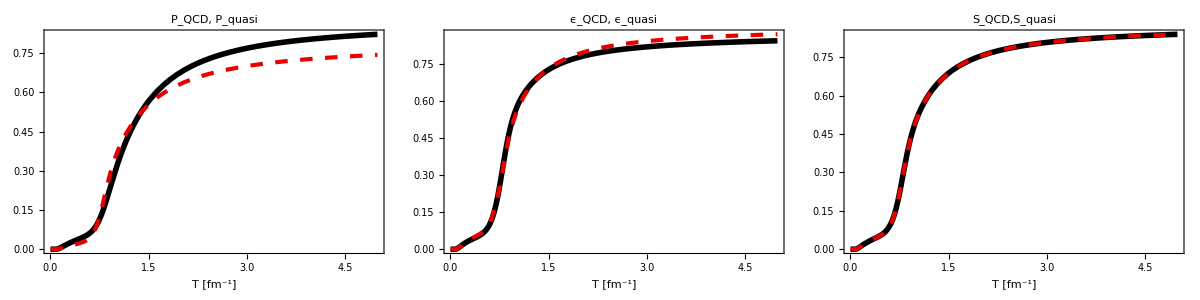

```mathematica
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]] (*-B0Quasifunc[T]*);
Equasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*(3.0*BesselK[2,zQuasifunc[T]]+zQuasifunc[T]*BesselK[1,zQuasifunc[T]])(*+B0Quasifunc[T]*);

SQuasi[T_]=(Pquasi[T]+Equasi[T])/T;

Grid[{{Plot[{PInt[T]/(sFac T^4/3),Pquasi[T]/(sFac T^4/3)},{T,.001,5},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"P_QCD, P_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{edInt[T]/(sFac T^4),Equasi[T]/(sFac T^4)},{T,.001,5},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"ϵ_QCD, ϵ_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{SInt[T]/(4*sFac*T^3/3),SQuasi[T]/(4*sFac*T^3/3)},{T,.001,5},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"S_QCD,S_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
```

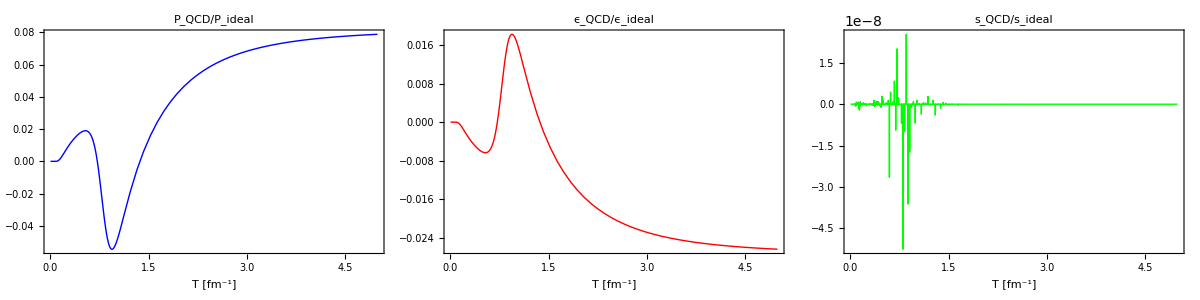

```mathematica
Grid[{{Plot[{(PInt[T]-Pquasi[T])/(sFac T^4/3)},{T,.001,5},PlotStyle->Blue,ImageSize->380,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"P_QCD/P_ideal",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{(edInt[T]-Equasi[T])/(sFac T^4)},{T,.001,5},PlotStyle->Red,ImageSize->380,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"ϵ_QCD/ϵ_ideal",BaseStyle->{FontSize->16},AspectRatio->0.75],Plot[{(SInt[T]-SQuasi[T])/(4*sFac T^4/3)},{T,.001,5},PlotStyle->Green,ImageSize->380,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"s_QCD/s_ideal",BaseStyle->{FontSize->16},AspectRatio->0.75]
}}]
```

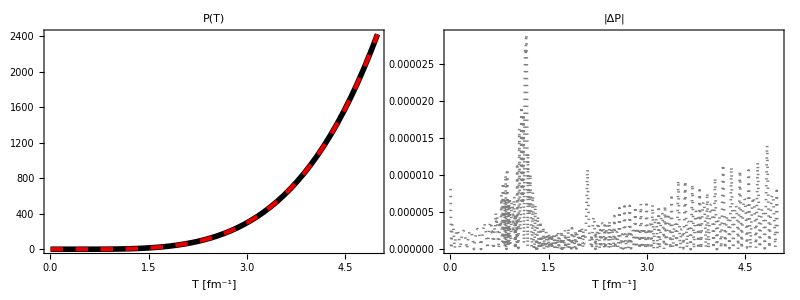

```mathematica
(* Fitting the quasiparticle kinetic pressure (B = 0) *)
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]];  (*kinetic only; no bag term*)
Pquasidata=Table[{T,Pquasi[T]},{T,0.001,5,0.0005}];
n = 12;
Pquasifit[T_]=rationalPolyFit[Pquasidata,n,n]/.{x->T};

Grid[{{
Plot[{Pquasi[T],Pquasifit[T]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["P(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[Pquasi[T]-Pquasifit[T]]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔP|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
Pquasifit[T]//CForm;
```

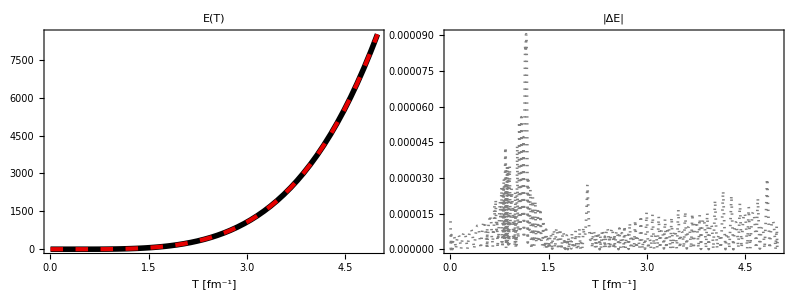

```mathematica
(* Fitting the quasiparticle kinetic energy density (B = 0) *)
Equasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*(3.0*BesselK[2,zQuasifunc[T]]+zQuasifunc[T]*BesselK[1,zQuasifunc[T]]);  (*kinetic only; no bag term*)
Equasidata=Table[{T,Equasi[T]},{T,0.001,5,0.0008}];
n = 12;
Equasifit[T_]=rationalPolyFit[Equasidata,n,n]/.{x->T};
Grid[{{
Plot[{Equasi[T],Equasifit[T]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["E(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[Equasi[T]-Equasifit[T]]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔE|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
Equasifit[T]//CForm;
```

```mathematica
(*Quasiparticle kinetic pressure as a function of lattice energy density*)

Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]];

LogTLogEDInt = Interpolation[eosData[[All,{2,1}]]];
TIntED[e_]=10^LogTLogEDInt[Log[10,e]];

PquasiED[e_]=Pquasi[TIntED[e]];

cs2quasi[e_]=PquasiED'[e];

PIntED[e_]=PInt[TIntED[e]];
cs2check[e_]=PIntED'[e];



Tmax = 5.0;
Tmin = 0.001;
dT = 0.0005;
Tsteps = (Tmax-Tmin)/dT
```

9998.

```mathematica
Tgrid=Table[0.001+i*0.0005,{i,0,Tsteps}];
egrid=Table[edInt[Tgrid[[i]]],{i,1,Tsteps+1}];

cs2quasidata=Table[{egrid[[i]],cs2quasi[egrid[[i]]]},{i,1,Tsteps+1}];
n = 12;
cs2quasifit[e_]=rationalPolyFit[cs2quasidata,n,n]/.{x->e};
```

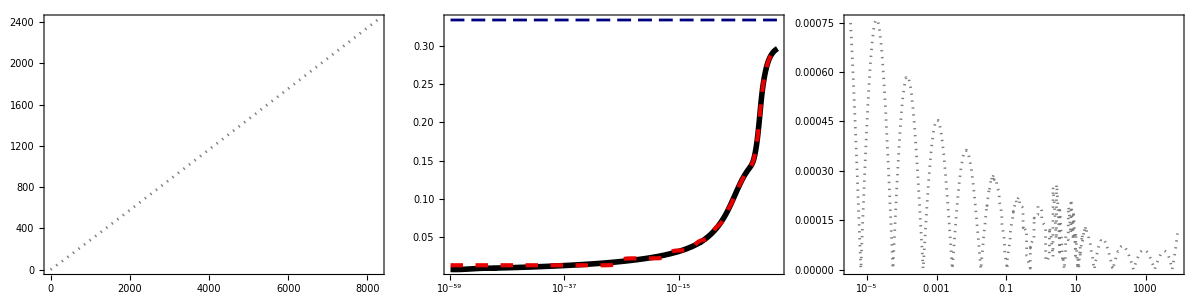

(5.737954698914043e-78 + 3.520811363350305e-51*e + 7.307099599076666e-34*Power(e,2) + 9.834260041073485e-22*Power(e,3) + 
     5.459922620643493e-13*Power(e,4) + 1.147614896634912e-6*Power(e,5) + 0.030489639274808255*Power(e,6) + 15.418025380394672*Power(e,7) + 
     71.66454223696546*Power(e,8) + 42.4246262263939*Power(e,9) + 7.084116096494792*Power(e,10) + 0.11501628671300337*Power(e,11) + 
     0.00006857951692360045*Power(e,12))/
   (4.2219927464162e-76 + 1.557880437858651e-49*e + 2.2180331194628334e-32*Power(e,2) + 2.117221841405106e-20*Power(e,3) + 
     8.362452841635948e-12*Power(e,4) + 0.000012749110730197145*Power(e,5) + 0.2587577951798222*Power(e,6) + 111.12044773806566*Power(e,7) + 
     449.15253462074963*Power(e,8) + 191.27260853909084*Power(e,9) + 27.145808442491013*Power(e,10) + 0.3989402274761829*Power(e,11) + 
     0.00023041833267698115*Power(e,12))

```mathematica
Grid[{{Plot[{PquasiED[e]},{e,edInt[0.001],edInt[5.0]}],LogLinearPlot[{cs2quasi[e],cs2quasifit[e],1.0/3.0},{e,edInt[0.001],edInt[5.0]}],LogLinearPlot[{Abs[cs2quasi[e]-cs2quasifit[e]]},{e,edInt[0.1],edInt[5.0]}]}}]

cs2quasifit[e]//CForm
```

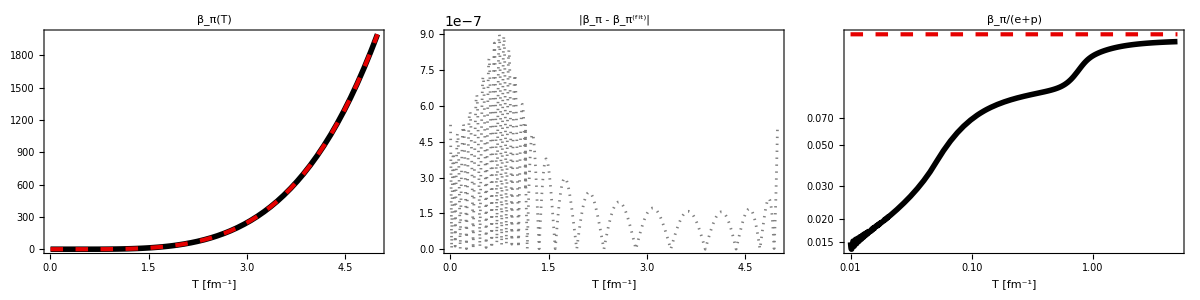

```mathematica
betapiDataRaw=Import[wd<>"/betapiplot.dat"];
betapiData= Take[betapiDataRaw,{2,Length[betapiDataRaw]}];
betapi = Interpolation[betapiData[[All,{1,2}]]];
n = 14;
betapifit[T_]=rationalPolyFit[betapiData,n,n]/.{x->T};
betapiconformal[T_]=0.2*(edInt[T]+PInt[T]);

Grid[{{Plot[{betapi[T],betapifit[T]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betapi[T]-betapifit[T]]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["|β_π - β_π^(fit)|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLogPlot[{betapi[T]/(edInt[T]+PInt[T]),betapiconformal[T]/(edInt[T]+PInt[T])},{T,0.01,5},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π/(e+p)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
betapifit[T]//CForm;
```

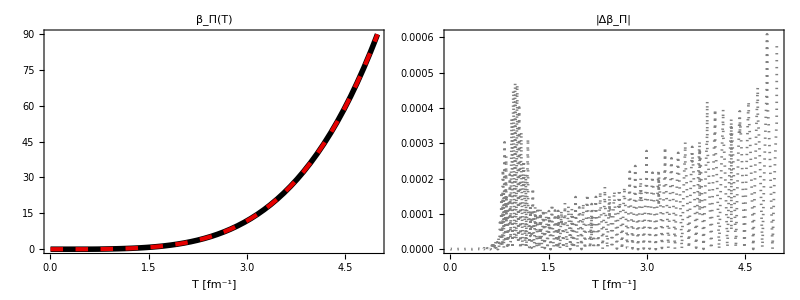

(0.000010905760709167861 - 0.004683989457592804*T + 0.24754406178287106*Power(T,2) - 4.885445624666566*Power(T,3) + 50.09614745592617*Power(T,4) - 
     307.7032088120906*Power(T,5) + 1199.345936356805*Power(T,6) - 3134.7810945740785*Power(T,7) + 5705.875248385415*Power(T,8) - 
     7386.615125073046*Power(T,9) + 6838.523042759372*Power(T,10) - 4474.354253326277*Power(T,11) + 1997.5827901556845*Power(T,12) - 
     562.5161507019361*Power(T,13) + 79.67974066311064*Power(T,14))/
   (-40.624628025755804 + 107.6723401385496*T - 23.19390975206659*Power(T,2) - 95.34803927008286*Power(T,3) - 47.579669340536825*Power(T,4) + 
     66.02920940835048*Power(T,5) + 194.0662782679704*Power(T,6) + 14.784256174958234*Power(T,7) - 637.8693894211432*Power(T,8) + 
     806.4328841485209*Power(T,9) - 469.0986465043204*Power(T,10) + 137.20558809601678*Power(T,11) - 9.98223482226815*Power(T,12) + 
     0.30712590209276874*Power(T,13) - 0.002441723962961617*Power(T,14))

```mathematica
(*betaPiDataRaw=Import[wd<>"/betabulkplot.dat"];
betaPiData= Take[betaPiDataRaw,{3,Length[betaPiDataRaw]}];*)
(*betaPi = Interpolation[betaPiData[[All,{1,2}]]];
betaPiconformal[T_]=14.55*(1.0/3.0-cs2Int[T])^2*(edInt[T]+PInt[T]);*)
(*betaPiconformal[T_]=15*(1.0/3.0-cs2quasi[edInt[T]])^2*(edInt[T]+PInt[T]);*)
(*n = 14;
betaPifit[T_]=rationalPolyFit[betaPiData,n,n]/.{x->T};*)

betabulk[T_] = 5.0/3.0*betapi[T]-cs2quasi[edInt[T]]*(edInt[T]+PInt[T]);
betabulkdata=Table[{T,betabulk[T]},{T,0.001,5.0,0.0005}];
n = 14;
betabulkfit[T_]=rationalPolyFit[betabulkdata,n,n]/.{x->T};
Grid[{{
Plot[{betabulk[T],betabulkfit[T]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["β_Π(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betabulk[T]-betabulkfit[T]]},{T,0.001,5},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δβ_Π|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

betabulkfit[T]//CForm
```